# Generation of descriptors for Active Learning

Joshua Schrier <jschrier@fordham.edu>

## Background information and insights

10 Apr 2020.

Our goal is to build a dataset that looks as close as possible to the DRP paper: “Machine-learning assisted materials discovery using failed experiments” https://www.nature.com/articles/nature17439   Details of the descriptors used is contained in Tables S1-S4 of the Supplementary Information.

The documentation for the current perovskites dataset is https://docs.google.com/document/d/1PML1dJRIxMyVd1Q_Iq6chFyTUjIHyo7IWsxKZsuK7og/edit#

We’re using the Crank50 dataset (25 Feb 2020)
https://drive.google.com/drive/folders/1pFSuCmS6teZzl4DvFum_ 6wpxVujQF1kf

(17 Apr 2020) Added organic InChI key to facilitate LOO training

(02 Jul 2020) Dealing with changes to the ESCALATE v2 report output.  https://github.com/darkreactions/ESCALATE_report/issues/65

(03 Jul 2020) Processing updated file (fixed so that it has all column names) received from Shekar V.

### Problems discovered during this exercise (Apr 2020)

Documentation for the features describes features that aren’t there(!)—but relatively minor.  Comments posted on relevant documents.

Lack of documentation on what the `_raw_V1-mmol_*_final `features mean (i.e., SolUD); (commented in documentation)

Problem of the InChIKey of 1,3-dap-iodide (commented on chemical inventory spreadsheet)

The ambient lab temperature sensors are goofy (noted below, posted to slack for TA3 team)—for now we’re excluding this information.

However, we have included ambient lab relative humidity, as Zhi/Emory believe that these data are reasonable.

Experiment performance date is *not* reported in the dataset and there are data-integrity problems with how it is recorded (described below)

_raw_datecompleted and _raw_timecompleted_UTC are both uniformly zero (“0”) in the dataset.  None of this information appears to be passed through

Data integrity:  “_raw_reagent_*_date” information appears to be exactly the same as the “_raw_date_created” based on a spot-check.  I suspect that this is a data collection problem.  For example, examining https://docs.google.com/spreadsheets/d/1J6RkTl1ZMrtgHJL53_ 93BWNfY4Kjwpawu3OVwWiRWCg/edit#gid=0 it appears that these

Formatting bugs posted on #escalate-dev on 02 March 2020 still remain (not surprising as this dataset hasn’t been updated ...but what are we waiting for?)

### Comments for users

Data set summary

restricted to LBL experiments, with WF1.1 chemistry, with a complete description of outcome (deleted cases without observed outcomes)

only lead iodide reactions—so no inorganic descriptors are relevant

the stoichiometric features are expanded relative to the DRP Nature 2015 paper, because we have more types of things.

I’ve tried to make everything ready for ML.

AFAIK, there is no missing data in any column—and conseuquently, no encoding for missing data

Values are not standardized in the column.

There may be correlations between some of the columns that you'll want to feature-select out before use.

Solvent identities are one-hot-encoded as "_solv_" feature

Logical attributes are coded 0,1

There are a few features that you don’t want to learn on:

“name” should be dropped (unique identifier for if we want to look things up.

"_raw_modelname" column—this lets you select the sampler used.  Be sure to drop this if you don't care (or select on those field values)

“_out_crystalscore” is the value to predict.  Our standard 1,2,3,4 coding is used.

## Import and sanitize the data

```mathematica
SetDirectory@NotebookDirectory[]
data=Import["~/Downloads/WF1_iodides_7_2_2020.csv","Dataset",(*"SkipLines"->4,*) (*comment lines omitted in Shekar's dump*)"HeaderLines"->1];
```

/Users/jschrier/Dropbox/journals/science/2020.04.10_data_for_AL

### Preliminary analysis

We want to restrict ourselves to WF1.1, performed at LBL,  having a crystal score

NOTE:  IP has changed the names

```mathematica
(#->data[CountsBy[#]])&/@{"_raw_expver","_raw_lab","_out_crystalscore"}//Association//Dataset
```

### Preparatory Data cleansing

```mathematica
data=Query[Select[ (#["_raw_expver"]==1.1) && (#["_raw_lab"]=="LBL") && (#["_out_crystalscore"]>0)&&#[ToLowerCase@"_raw_mmol_RQQRAHKHDFPBMC-UHFFFAOYSA-L"]>0&]]@data; (*must contain lead iodide...*)
```

```mathematica
data
```

Dataset[<>]

### What keys are present in the dataset? (to facilitate browsing)

```mathematica
Keys@First@data
keys=Normal[%];
```

```mathematica
data[DeleteDuplicatesBy["_raw_modelname"]][All,"_raw_modelname"]//Normal//Sort
```

{Additional Data,escalate_ExpertQuasiRandom_1.1,escalate_ExpertQuasiRandom_1.2,escalate_ExpertQuasiRandom_2.4,escalate_ExpertQuasiRandom_2.5,escalate_ManualSpecification_1,escalate_MathematicaMultiStock_1.2,escalate_MathematicaUniformRandom_1,escalate_MathematicaUniformRandom_1.1,escalate_MathematicaUniformRandom_1.2,escalate_Prototyping_0,escalate_ReproducabilityTesting_0,escalation_BOGPall_1.0,escalation_BOGPamine_1.0,escalation_BOGPamine_1.1,escalation_BOGPamine_1.2,escalation_BOGPamine_1.3,escalation_BOGPamine_1.4,escalation_BOGPamine_1.5,escalation_CombinatorialFusionAnomalies_1.0,escalation_HC.RL_0,escalation_HC.RL_1,escalation_NumpyRandom_1.0,escalation_randombaseline_1.0,escalation_replicates_1.0,Reproducing_Runs,Reproducing_Runs-Temp,testharness_gradientboostedtree_1.0,testharness_LogisticRegression_1.0,testharness_RandomForestClassifier_1,testharness_rxnIntuitionSVM_1.0,testharness_SVMRadialBasis_1.0,testharness_SVM-RBC-rxnonly_1.0}

## Turn this into Nature DRP paper like descriptors

### Table S1: Inorganic properties

Comment: These are all irrelevant for the perovskites problem, as there is only one type of inorganic (lead iodide) used in these reactions.

### Table S2: Stoichiometry ratio properties

Comment: Many of these have to change, because of the nature of the problem.  We have more types of solvents (and I will try to include that generally, as well as including a one-hot encoding of which solvent is present).  The “acid” can be considered as either a contributor to the solvent or not, so we include those ratios.  But the same general idea is preserved.

#### Define functions to process the data:

```mathematica
(*convert an input molecule name (human readable) into the descriptor column name*)
(*convert to lowercase....*)
mmolFeatureName[name_String]:=StringTemplate["_raw_mmol_``"]@ToLowerCase@MoleculeProperty["InChIKey"]@Molecule[name]
SetAttributes[mmolFeatureName,Listable];

(*perform the stoichiometric calculations on each row*)
Clear[stoichiometricCalc];

stoichiometricCalc[row_]:=With[
{acid=Lookup[row,mmolFeatureName["formic acid"]],
solventVec=Lookup[row,mmolFeatureName@{"gamma butyrolactone","dimethyl sulfoxide","Dimethylformamide"}],
inorganic=Lookup[row,mmolFeatureName["lead diiodide"]],
organic=Lookup[row,ToLowerCase@StringTemplate["_raw_mmol_``"]@row["_raw_organic_0_inchikey"]]},
With[
{solvent=Total[solventVec],
liquids=acid+Total[solventVec],
unitStep=If[#>0,1,0]& (*define your own, as Mathematica's UnitStep[0]=1*)
},

<|"name"->row["name"], (*existing features to retain*)
"_rxn_organic-inchikey"->row["_raw_organic_0_inchikey"],
"_rxn_M_acid"->row["_rxn_molarity_acid"],
"_rxn_M_inorganic"->row["_rxn_molarity_inorganic"],
"_rxn_M_organic"->row["_rxn_molarity_organic"],

"_solv_GBL"->unitStep@solventVec[[1]], (*one-hot-encoded solvent identifier*)
"_solv_DMSO"->unitStep@solventVec[[2]],
"_solv_DMF"->unitStep@solventVec[[3]],

"_stoich_mmol_org"->organic, (*just raw number of mmols; might consider ignoring this, but we used it in Polyhedron 2016 & MSDE 2018*)
"_stoich_mmol_inorg"->inorganic,
"_stoich_mmol_acid"->acid,
"_stoich_mmol_solv"->solvent,

"_stoich_org/solv"->organic/solvent, (*stoichiometric ratios analogous to Nature 2015 paper*)
"_stoich_inorg/solv"->inorganic/solvent,
"_stoich_acid/solv"->acid/solvent,
"_stoich_org+inorg/solv"->(organic+inorganic)/solvent,
"_stoich_org+inorg+acid/solv"->(organic+inorganic+acid)/solvent,
"_stoich_org/liq"->organic/liquids,
"_stoich_inorg/liq"->inorganic/liquids,
"_stoich_org+inorg/liq"->(organic+inorganic)/liquids,
"_stoich_org/inorg"->organic/inorganic,
"_stoich_acid/inorg"->acid/inorganic|>
]]
```

```mathematica
(*sanity checks*)
row=Normal@First@data;
stoichiometricCalc[row]
```

<|name→2018-07-06T15_40_16.425303+00_00_LBL_A1,_rxn_organic-inchikey→XFYICZOIWSBQSK-UHFFFAOYSA-N,_rxn_M_acid→6.2196,_rxn_M_inorganic→0.249044,_rxn_M_organic→0.721707,_solv_GBL→1,_solv_DMSO→0,_solv_DMF→0,_stoich_mmol_org→0.470553,_stoich_mmol_inorg→0.162377,_stoich_mmol_acid→4.05518,_stoich_mmol_solv→5.81796,_stoich_org/solv→0.0808794,_stoich_inorg/solv→0.0279096,_stoich_acid/solv→0.697011,_stoich_org+inorg/solv→0.108789,_stoich_org+inorg+acid/solv→0.8058,_stoich_org/liq→0.0476599,_stoich_inorg/liq→0.0164463,_stoich_org+inorg/liq→0.0641062,_stoich_org/inorg→2.89791,_stoich_acid/inorg→24.9739|>

#### Run it!

```mathematica
s2Data=Map[stoichiometricCalc,data];
First@s2Data (*see an example*)
```

### Table S3: Reaction conditions

What temperature and reaction conditions do we have in our dataset?

```mathematica
Select[StringStartsQ["_rxn"]]@keys
```

{_rxn_temperatureC_actual_bulk,_rxn_mixingtime1_s,_rxn_mixingtime2_s,_rxn_preheattemperature_c,_rxn_reactiontime_s,_rxn_stirrate_rpm,_rxn_temperature_c,_rxn_M_acid,_rxn_M_inorganic,_rxn_M_organic,_rxn_molarity_solvent,_rxn_organic-inchikey}

#### Comments:

Leak and slowcool are not relevant

Initial pH information is present in the _rxn_M acid feature presented in stoichiometry data

There are some additional temperature parameters

Comment:  There are some additional temperatures and times specified.  However, most of these have no variation, and some are highly correlated

Comment (02 July 2020):  Modifying property names to match the “all-lower case” change that was made in IP’s last version  There’s something else that is screwy about the _rxn_preheattemperature_c values (they’re be interpreted with Conjugate?  But we don’t have to figure that out now....

#### Implementation:

```mathematica
s3properties={"_rxn_temperatureC_actual_bulk","_rxn_mixingtime1_s","_rxn_mixingtime2_s","_rxn_preheattemperature_c","_rxn_reactiontime_s","_rxn_stirrate_rpm","_rxn_temperature_c"}
```

{_rxn_temperatureC_actual_bulk,_rxn_mixingtime1_s,_rxn_mixingtime2_s,_rxn_preheattemperature_c,_rxn_reactiontime_s,_rxn_stirrate_rpm,_rxn_temperature_c}

```mathematica
(#->(data[All,#]//Normal//Variance))&/@s3properties
```

{_rxn_temperatureC_actual_bulk→1/71732430(49044 (-211907-19 )+4200 (-186497-19 )+7680 (-101797-19 )+7968 (-76387-19 )+24395 (-59447-19 )+2068 (16783-19 )+661770 (25253-19 )+10560 (152303-19 )+11712 (253943-19 )+19 (-779397+8451 ) Conjugate[]),_rxn_mixingtime1_s→0,_rxn_mixingtime2_s→0,_rxn_preheattemperature_c→(7680 (669920-8374 )+8374 (-7680+96 ) Conjugate[])/71732430,_rxn_reactiontime_s→2120774400000/797027,_rxn_stirrate_rpm→0,_rxn_temperature_c→269292280/2391081}

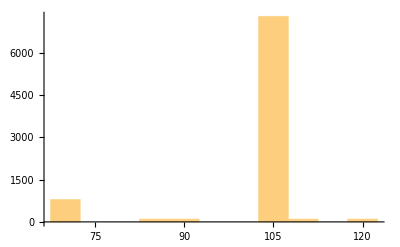
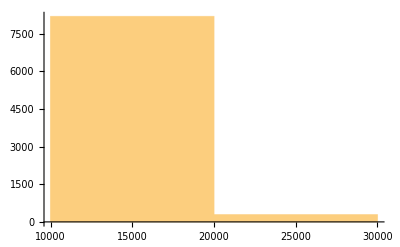
{_rxn_temperature_c→-Graphics-,_rxn_reactiontime_s→-Graphics-}

```mathematica
(#->(data[All,#]//Normal//Histogram))&/@{"_rxn_temperature_c","_rxn_reactiontime_s"}
```

```mathematica
s3Data=data[All,{"name","_rxn_temperature_c","_rxn_reactiontime_s"}];
First@s3Data (*example*)
```

## Table S4: Organic Properties

```mathematica
Select[StringContainsQ["_feat_organic_0_"]]@Normal@Keys@First@data
```

{_feat_organic_0_accsitecount_std,_feat_organic_0_aliphaticatomcount_std,_feat_organic_0_aliphaticringcount_std,_feat_organic_0_aromaticatomcount_std,_feat_organic_0_aromaticringcount_std,_feat_organic_0_asa+_std,_feat_organic_0_asa-_std,_feat_organic_0_asa_std,_feat_organic_0_asah_std,_feat_organic_0_asap_std,_feat_organic_0_asavdwp_std,_feat_organic_0_atomcount_c_std,_feat_organic_0_atomcount_n_std,_feat_organic_0_avgpol_std,_feat_organic_0_balabanindex_std,_feat_organic_0_bondcount_std,_feat_organic_0_carboaliphaticringcount_std,_feat_organic_0_carboaromaticringcount_std,_feat_organic_0_carboringcount_std,_feat_organic_0_chainatomcount_std,_feat_organic_0_chiralcentercount_std,_feat_organic_0_cyclomaticnumber_std,_feat_organic_0_donsitecount_std,_feat_organic_0_fr_amidine,_feat_organic_0_fr_dihydropyridine,_feat_organic_0_fr_guanido,_feat_organic_0_fr_halogen,_feat_organic_0_fr_piperdine,_feat_organic_0_fr_piperzine,_feat_organic_0_fr_pyridine,_feat_organic_0_hacceptorcount_std,_feat_organic_0_hdonorcount_std,_feat_organic_0_heteroaliphaticringcount_std,_feat_organic_0_heteroaromaticringcount_std,_feat_organic_0_hyperwienerindex_std,_feat_organic_0_largestringsize_std,_feat_organic_0_maximalprojectionarea_std,_feat_organic_0_maximalprojectionradius_std,_feat_organic_0_maximalprojectionsize_std,_feat_organic_0_minimalprojectionarea_std,_feat_organic_0_minimalprojectionradius_std,_feat_organic_0_minimalprojectionsize_std,_feat_organic_0_molpol_std,_feat_organic_0_organoammoniummolecularweight_std,_feat_organic_0_protpsa_std,_feat_organic_0_refractivity_std,_feat_organic_0_ringatomcount_std,_feat_organic_0_rotatablebondcount_std,_feat_organic_0_saltmolecularweight,_feat_organic_0_smallestringsize_std,_feat_organic_0_vanderwaalsvolume_std,_feat_organic_0_wienerindex_std,_feat_organic_0_wienerpolarity_std}

Comment:  There is only one organic in each of these, so we can dispense with the min/max/mean aspects

Commnt (02 Jul 2020) : IP  has really mucked this up.  Waiting on Shekar to reimplement ASA.

```mathematica
Clear[fixIP]
fixIP[in_]:=If[StringStartsQ["_feat"]@#,StringInsert[#,"_std",-1],#]&/@StringReplace["_feat_"->"_feat_organic_0_"]/@ToLowerCase/@in
```

```mathematica
s4properties=fixIP@{"_feat_avgpol","_feat_refractivity","_feat_maximalprojectionArea","_feat_MaximalProjectionRadius","_feat_maximalprojectionsize","_feat_MinimalProjectionArea","_feat_MinimalProjectionRadius","_feat_minimalprojectionsize","_feat_MolPol","_feat_asavdwp",(*this was renamed*) "_feat_asa" (*added back by shekar*),"_feat_ASAH",(*got renamed*)"_feat_ASAP",(*got renamed*)"_feat_ASA-","_feat_ASA+","_feat_ProtPSA",(*also renamed*)"_feat_Hacceptorcount","_feat_Hdonorcount"};
```

```mathematica
s4properties
```

{_feat_organic_0_avgpol_std,_feat_organic_0_refractivity_std,_feat_organic_0_maximalprojectionarea_std,_feat_organic_0_maximalprojectionradius_std,_feat_organic_0_maximalprojectionsize_std,_feat_organic_0_minimalprojectionarea_std,_feat_organic_0_minimalprojectionradius_std,_feat_organic_0_minimalprojectionsize_std,_feat_organic_0_molpol_std,_feat_organic_0_asavdwp_std,_feat_organic_0_asa_std,_feat_organic_0_asah_std,_feat_organic_0_asap_std,_feat_organic_0_asa-_std,_feat_organic_0_asa+_std,_feat_organic_0_protpsa_std,_feat_organic_0_hacceptorcount_std,_feat_organic_0_hdonorcount_std}

```mathematica
Sort@Select[StringStartsQ["_raw_organic"]]@keys
```

{_raw_organic_0_smiles,_raw_organic_0_smiles_standardized,_raw_organic_0_types}

```mathematica
s4Data=data[All,Join[{"name"},s4properties]];
(*example of what this looks like*)
Normal@First@s4Data
```

<|name→2018-07-06T15_40_16.425303+00_00_LBL_A1,_feat_organic_0_avgpol_std→6.09,_feat_organic_0_refractivity_std→25.96,_feat_organic_0_maximalprojectionarea_std→22.85,_feat_organic_0_maximalprojectionradius_std→3.3,_feat_organic_0_maximalprojectionsize_std→5.17,_feat_organic_0_minimalprojectionarea_std→17.09,_feat_organic_0_minimalprojectionradius_std→2.59,_feat_organic_0_minimalprojectionsize_std→6.59,_feat_organic_0_molpol_std→5.88,_feat_organic_0_asavdwp_std→112.02,_feat_organic_0_asa_std→215.57,_feat_organic_0_asah_std→164.65,_feat_organic_0_asap_std→50.92,_feat_organic_0_asa-_std→61.53,_feat_organic_0_asa+_std→154.04,_feat_organic_0_protpsa_std→27.64,_feat_organic_0_hacceptorcount_std→0.,_feat_organic_0_hdonorcount_std→1.|>

#### Sanity check: They actually do vary...

```mathematica
s4Data[Variance,s4properties]
```

## Table X1: Other things we have come to find important...that are trivially in the dataset

Comment: There are two “molecular weights” reported; this one (“_raw_standard_molweight”) is for the organic component of the salt only, which is more relevant

ChainAtomCount: From Polyhedron 2016 paper
RingAtomCount: In Polyhedron2016 we used this as a binary variable (ring or not).  Leaving it numerical here.

Comment (02 July 2020):  it appears that IP has changed “_raw_standard_molweight” --> “_raw_standard_molweight”

```mathematica
addtlProperties=fixIP@{"_feat_RotatableBondCount","_feat_organoammoniummolecularweight","_feat_AtomCount_N","_feat_BondCount","_feat_ChainAtomCount","_feat_RingAtomCount","_raw_modelname"};

sX1Data=data[All,Join[{"name"},addtlProperties]];
(*example of what this looks like*)
Normal@First@sX1Data
```

<|name→2018-07-06T15_40_16.425303+00_00_LBL_A1,_feat_organic_0_rotatablebondcount_std→0.,_feat_organic_0_organoammoniummolecularweight_std→46.092,_feat_organic_0_atomcount_n_std→1.,_feat_organic_0_bondcount_std→10.,_feat_organic_0_chainatomcount_std→3.,_feat_organic_0_ringatomcount_std→0.,_raw_modelname→escalate_ExpertQuasiRandom_1.1|>

## Table X2: Yet more things that we have to calculate

Comments:  

Warning:  Raw VialSite is an alphanumeric identifier...cconvert to “edge”/”Center” representation

I don’t believe the values being used, because I don’t trust that IP has neutralized the molecules correctly, so the SMARTS pattern will break.  So we do it below.

primary ammonium—neutralize the molecule and compute
secondary ammonium
cyclic structure (binary)—[exclude this...it’s above]
Maximal projection area/nitrogen [done]

```mathematica
Select[StringContainsQ["smiles"]]@keys
```

{_raw_acid_0_smiles,_raw_inorganic_0_smiles,_raw_organic_0_smiles,_raw_organic_0_smiles_standardized,_raw_solvent_0_smiles,_raw_solvent_1_smiles}

```mathematica
data[[1,{"_raw_organic_0_smiles","_raw_organic_0_smiles_standardized"}]]
```

### Pre-compute the neutralized molecules, so we don’t have to do this thousands of time

```mathematica
(*follows the RDKit standard for assigning primary/secondary amines: https://github.com/rdkit/rdkit/blob/master/Data/FragmentDescriptors.csv*)
moleculeFunctionalGroupData[smiles_String]:=With[
{mol=ResourceFunction["MoleculeNeutralize"][smiles,"Molecule"]},
smiles-><|
"_feat_NH2"->MoleculeContainsQ[MoleculePattern["[NH2,nH2]"]]@mol,
"_feat_NH1"->MoleculeContainsQ[MoleculePattern["[NH1,nH1]"]]@mol|>]

SetAttributes[moleculeFunctionalGroupData,Listable]

moleculeData=Association@moleculeFunctionalGroupData@Normal@data[DeleteDuplicatesBy["_raw_organic_0_smiles"],"_raw_organic_0_smiles_standardized"];
```

```mathematica
Sort@Select[StringStartsQ["_feat_organ"]]@keys
```

{_feat_organic_0_accsitecount_std,_feat_organic_0_aliphaticatomcount_std,_feat_organic_0_aliphaticringcount_std,_feat_organic_0_aromaticatomcount_std,_feat_organic_0_aromaticringcount_std,_feat_organic_0_asah_std,_feat_organic_0_asap_std,_feat_organic_0_asa-_std,_feat_organic_0_asa+_std,_feat_organic_0_asavdwp_std,_feat_organic_0_atomcount_c_std,_feat_organic_0_atomcount_n_std,_feat_organic_0_avgpol_std,_feat_organic_0_balabanindex_std,_feat_organic_0_bondcount_std,_feat_organic_0_carboaliphaticringcount_std,_feat_organic_0_carboaromaticringcount_std,_feat_organic_0_carboringcount_std,_feat_organic_0_chainatomcount_std,_feat_organic_0_cyclomaticnumber_std,_feat_organic_0_donsitecount_std,_feat_organic_0_fr_amidine,_feat_organic_0_fr_guanido,_feat_organic_0_fr_halogen,_feat_organic_0_fr_piperdine,_feat_organic_0_fr_piperzine,_feat_organic_0_fr_pyridine,_feat_organic_0_hacceptorcount_std,_feat_organic_0_hdonorcount_std,_feat_organic_0_heteroaliphaticringcount_std,_feat_organic_0_heteroaromaticringcount_std,_feat_organic_0_hyperwienerindex_std,_feat_organic_0_largestringsize_std,_feat_organic_0_maximalprojectionarea_std,_feat_organic_0_maximalprojectionradius_std,_feat_organic_0_maximalprojectionsize_std,_feat_organic_0_minimalprojectionarea_std,_feat_organic_0_minimalprojectionradius_std,_feat_organic_0_minimalprojectionsize_std,_feat_organic_0_molpol_std,_feat_organic_0_organoammoniummolecularweight_std,_feat_organic_0_protpsa_std,_feat_organic_0_refractivity_std,_feat_organic_0_ringatomcount_std,_feat_organic_0_rotatablebondcount_std,_feat_organic_0_saltmolecularweight,_feat_organic_0_smallestringsize_std,_feat_organic_0_vanderwaalsvolume_std,_feat_organic_0_wienerindex_std,_feat_organic_0_wienerpolarity_std}

### Build the datasets

```mathematica
plateEdgeQ[siteLabel_String]:=StringStartsQ[siteLabel,"A"|"H"]||StringEndsQ[siteLabel,(LetterCharacter~~"1")|(LetterCharacter~~"12")]

Clear[addtlCalc]
ClearAttributes[addtlCalc,Listable]
addtlCalc[moleculeLookup_Association][row_]:=With[
{amineData=Lookup[moleculeLookup,row["_raw_organic_0_smiles_standardized"],Missing]},
<|
"name"->row["name"],
"_feat_primaryAmine"->Boole@amineData["_feat_NH2"],
"_feat_secondaryAmine"->Boole@amineData["_feat_NH1"],
"_rxn_plateEdgeQ"->Boole@plateEdgeQ@row["_raw_vialsite"],
"_feat_maxproj_per_N"->row["_feat_organic_0_maximalprojectionarea_std"]/row["_feat_organic_0_atomcount_n_std"],
"_feat_vdw_per_N"->row["_feat_organic_0_asavdwp_std"]/row["_feat_organic_0_atomcount_n_std"]
|>]
```

```mathematica
sX2Data=Map[addtlCalc[moleculeData],data ];
Normal@First@%
```

<|name→2018-07-06T15_40_16.425303+00_00_LBL_A1,_feat_primaryAmine→1,_feat_secondaryAmine→0,_rxn_plateEdgeQ→1,_feat_maxproj_per_N→22.85,_feat_vdw_per_N→112.02|>

## Table X3: Lab Temperature/Relative Humidity Data

Comment:  As you’ll see below there are a few missing values, but more worrisome are some of the goofy temperature values.  I find it hard to believe that these reflect reality, but on the other hand they occur only sporadically.  Conclusion from Zhi & Emory (slack discussion) is that there may be a bad connection to the thermocouple.  But the relative humidity data should be OK.  Some exploratory data analysis as I discovered/figured this out follows below.

Additionally, there are some serious errors in the dataset itself. 
 First:  All the _raw_timecompleted and _raw_datecompleted dates are empty/set to zero.  This is not being propogated.  To be 
 Second:  In some (haven’t check which) experiments, the operator didn’t both to specify the reaction performance fields e.g.,  https://docs.google.com/spreadsheets/d/1J6RkTl1ZMrtgHJL53_ 93BWNfY4Kjwpawu3OVwWiRWCg/edit#gid=0 
 
 So the most reliable way to check this would be to dig into the cases where we do have sensor data and use that date to add it back in. (Assuming it was right).  We won’t be able to do this for everything.

```mathematica
Select[StringContainsQ["_raw_reagent_0_date"]]@keys
```

{_raw_reagent_0_date}

```mathematica
data[[1,"_raw_reagent_2_date"]]
```

2018-11-04

```mathematica
Select[StringContainsQ["time"]]@keys
```

{_rxn_Mixingtime1_s,_rxn_Mixingtime2_s,_rxn_Reactiontime_s,_raw_timecompleted_UTC,_raw_timecreated_UTC}

```mathematica
Select[StringContainsQ["date"]]@keys
```

{_raw_datecompleted,_raw_datecreated,_raw_reagent_0_date,_raw_reagent_1_date,_raw_reagent_2_date,_raw_reagent_3_date,_raw_reagent_4_date,_raw_reagent_5_date,_raw_reagent_6_date,_raw_reagent_7_date,_raw_reagent_8_date}

```mathematica
jobs=data[GroupBy["_raw_jobserial"]]//Normal//Keys//Sort;
```

```mathematica
jobdates=data[DeleteDuplicatesBy["_raw_jobserial"],{"_raw_jobserial","_raw_reagent_0_date"}]
```

```mathematica
meanRHAndTemperature[jobserial_String]:=With[
{file=First[FileNames[ "/Volumes/GoogleDrive/My Drive/DARPA SD2 Perovskites/Science/4-Data-Iodides/"<>jobserial<>"/*Temperature_Humidity*"],Missing["no file"]]},
If[!MissingQ[file],
With[
{data=Map[Mean]@Transpose@Import[file,"Data"][[All,{3,5}]]}, (*annoyingly, these files don't have headers*)
<|"_raw_jobserial"->jobserial,"_raw_RelativeHumidity"->data[[1]],"_raw_lab_temperature_C"->data[[2]]|>
],
(*else...return a missing identifier (-1)*)
<|"_raw_jobserial"->jobserial ,"_raw_RelativeHumidity"->-1,"_raw_lab_temperature_C"->-1|>
]
]

SetAttributes[meanRHAndTemperature,Listable];

environmentalData=Dataset@meanRHAndTemperature@jobs
```

```mathematica
Export["temperature_humidity_logs.csv",environmentalData[SortBy["_raw_jobserial"]]]
```

temperature_humidity_logs.csv

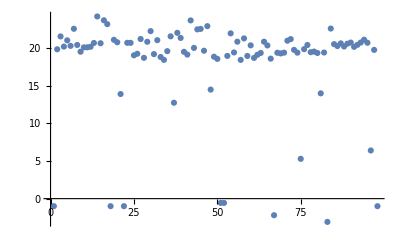

```mathematica
ListPlot[
environmentalData[SortBy["_raw_jobserial"],"_raw_lab_temperature_C"],
PlotRange->All]
```

```mathematica
environmentalData[Select[#["_raw_lab_temperature_C"]<15&]][SortBy["_raw_jobserial"]]
```

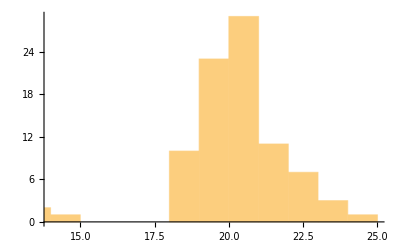

```mathematica
Histogram@environmentalData[SortBy["_raw_jobserial"],"_raw_lab_temperature_C"]
```

Update:  Zhi & Emory believe that this is a loose thermocouple connection, resulting in dodgy temperature data, but  relative humidity might be OK.

```mathematica
environmentalData
```

Comment: Don’t be so concerned that the first hundred are missing data (-1)....we hadn’t installed the sensor yet...

```mathematica
sX3Data=JoinAcross[data,environmentalData,"_raw_jobserial"][All,{"name","_raw_RelativeHumidity"}]
```

Dataset[<>]

## TODO: Things that aren’t present now, might be in chemdescriptor, can probably skip these for now

Min and Max pKA for the amines (Polyhedron 2016)

## Join it all together and export as CSV

```mathematica
Fold[JoinAcross[#1,#2,"name"]&]@{s2Data,s3Data,s4Data,sX1Data,sX2Data,sX3Data,data[All,{"name","_out_crystalscore"}]}
Export["0057.perovskitedata_DRPFeatures_2020-07-02.csv",%]
```

Dataset[<>]

0057.perovskitedata_DRPFeatures_2020-07-02.csv

## Visualize the amines

```mathematica
SetDirectory@NotebookDirectory[]
d=Import["0050.perovskitedata.csv","Dataset","SkipLines"->4,"HeaderLines"->1][All,"_raw_smiles_standard"]//Normal//DeleteDuplicates
```

/Volumes/SD/Dropbox/journals/science/2020.04.10_data_for_AL

{[NH3+]CCC1=CC=CC=C1,CCCC[NH3+],CC[NH3+],C[NH3+],NC(N)=[NH2+],CC(N)=[NH2+],[NH3+]C=N,[NH2+]1C=CN=C1,[NH3+]CC1=CC=CC=C1,CC(C)(C)C[NH3+],CC(C)[NH3+],CC(C)C[NH3+],C[NH2+]C,CCCCCCCCCCCC[NH3+],C1CC[NH2+]C1,[NH3+]CC[NH3+],COC1=CC=C([NH3+])C=C1,[NH3+]CCC[NH3+],CCC[NH3+],CC(C)CC[NH3+],[NH3+]CCC1=CC=C(F)C=C1,[NH3+]C1=CC=C(F)C=C1,[NH3+]CC1=CC=C(C=C1)C(F)(F)F,[NH3+]C1=CC=C(C=C1)C(F)(F)F,CC(C)(C)CC(C)(C)[NH3+],[NH3+]C1=CC=CC=C1,CC(C)(C)[NH3+],[NH3+]CC1=CC=C(F)C=C1,[NH3+]C1CCCCC1,C1C[NH+]2CCC1CC2,C1=CC=[NH+]C=C1,CC[NH2+]CC,CCCCCCCC[NH3+],C1COCC[NH2+]1,CCCCCC[NH3+],C1CC[NH2+]CC1,[NH3+]CC1CCCCC1,[NH3+]CCCC[NH3+],[NH3+]C1=CC=C([NH3+])C=C1,C[NH+](C)CC[NH3+],CC[NH+](CC)CCC[NH3+],C1C[NH2+]CC[NH2+]1,[NH3+]CC[NH+]1CCCC1,CC(C)[NH2+]C(C)C,C[NH+](C)CCC[NH3+],COC1=CC=C(CC[NH3+])C=C1}

```mathematica
MoleculePlot[Molecule[#]]&/@d//Partition[#,4]&//GraphicsGrid
```

-Graphics-